# Elementos Finitos - Domínio 1D com C.C. de Dirichlet by Caju - 2007 (LabMeC - FEC - Unicamp)

### Formulação variacional : a u'' + b u' + c u = f (x)

### Dados de Entrada:

```mathematica
a=-1;
b=1;
c=1;
Uexata=1/12*(5x-6*x^2+x^4);



(* Não Edite os dados abaixo *)
DUexata=D[Uexata,x];
f=a D[Uexata,{x,2}]+b D[Uexata,x]+c Uexata;
```

## Bloco

```mathematica
ElFin1D[degree_,n_,Ω0_,Ω1_,a_,b_,c_,var_,f_,Dirich0_,Dirich1_]:=Block[{ξ,coef,Ncoef,Fi,ϕi,ϕiL,ϕtemp,Nodes,ω0,ω1,h,α,Kloc,K,Floc,F,Un,erro,NormaEn,NormaL2,Index},
(* Building a table of polinomial function coefficients with the correct length, i.e.: {a,b,c,d,... } *)
coef=ToExpression[Table[FromCharacterCode[{97+i,97+i}],{i,0,degree}]];

(* Pol[ξ_] is an function that build the characteristic polinomial using the coefficients table, i.e.: a.x^0 + b.x^1 + c.x^2 + ... *)
Pol[ξ_]=∑_(k=0)^degree coef[[k+1]]*ξ^k;

(* Solving the polinomials linear sistem using boundary conditions, i.e.: Pol = 1 in analysed node, Pol = 0 in others nodes *)
(* The variables are the coefficients *)
(* Domain: [0,1] *)
Ncoef=Flatten[Table[NSolve[Table[Pol[j/degree]==KroneckerDelta[j-i],{j,0,degree}],coef],{i,0,degree}],1];

(* Substituting the numeric values of coefficients in the Pol[ξ_] functions *)
ϕi=Table[Pol[ξ]/.Ncoef[[i]],{i,1,degree+1}];

(* Establishing the Mapping Function from [Ω0,Ω1] domain to [0,1] domain *)
H=(Ω1-Ω0)/n;
h=H/degree;
ω0=Ω0;
ω1=ω0+H;
ξ=1/(ω1-ω0)*(var-ω0);
ϕiL=D[ϕi,var];

(*  ======= Local Computing =======  *)
Kloc=Table[0,{degree+1},{degree+1}];
For[i=1,i<=degree+1,i++,
       For[j=1,j<=degree+1,j++,
                  Kloc[[i,j]]=∫_ω0^ω1 (-a*ϕiL[[i]]*ϕiL[[j]]+b*ϕiL[[j]]*ϕi[[i]]+c*ϕi[[i]]*ϕi[[j]])ⅆvar ; 
         ];
   ];
K=Table[0,{n*degree+1},{n*degree+1}];
F=Table[0,{n*degree+1}];

(*  ======= Global Computing (Assembling) =======  *)
For[el = 1, el ≤ n,
	For[  px=1, px<=degree+1,px++,
		   For[       py=1,py<=degree+1,py++,
		   	     K[[(el-1)*degree+px,(el-1)*degree+py]]+=Kloc[[px,py]];
	                 ];
		    ϕtemp=ϕi/.var->var-(el-1)*H;
	              Floc=Table[∫_(ω0+(el-1)*H)^(ω1+(el-1)*H) f*ϕtemp[[i]]ⅆvar,{i,1,degree+1}];
	              F[[(el-1)*degree+px]]+=Floc[[px]];
              ];
          el++;
];

(* Dirichlet Boundary Conditions *)
For[  i=1,i<=n*degree+1,i++,
	K[[1,i]]=0;
	K[[n*degree+1,i]]=0;
    ];
K[[1,1]]=1;K[[n*degree+1,n*degree+1]]=1;
F[[1]]=Dirich0;F[[n*degree+1]]=Dirich1;

(* Solving Linear System *)
α=LinearSolve[N[K],N[F]];

(* Computing the Nodal Polinomials for All the Domain *)
ϕi[[1]]=Piecewise[{{ϕi[[degree+1]]/.var->(var+H),var≥ω0-H&&var≤ω0},{ϕi[[1]],var>ω0&&var<ω1}}];
ϕi[[degree+1]]=Piecewise[{{ϕi[[degree+1]],var≥ω0&&var≤ω1},{ϕi[[1]]/.var->(var-H),var>ω1&&var<ω1+H}}];
For[   i=2,i≤degree,i++,
	ϕi[[i]]=Piecewise[{{ϕi[[i]],var≥ω0&&var≤ω1}}];
];

Fi=Table[0,{degree*n+1}];
For[   i=1,i≤degree*n+1,i++,
	Index=Round[(h*(i-1)-Quotient[h*(i-1),H]*H)/h]+1;
	Fi[[i]]=ϕi[[Index]]/.{var->var-Quotient[h*(i-1),H]*H};
];
Un=N[Simplify[Chop[α.Fi]]];

Plot[Un,{var,Ω0,Ω1},PlotStyle->{Blue},Filling->Axis,PlotRange->All]
]
```

## Processamento

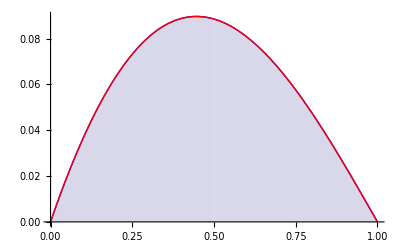

```mathematica
Degr=4;
Nelem=2;
Ini=0;
Fin=1;
DirichIni=Uexata/.x->Ini;
DirichFin=Uexata/.x->Fin;
ElFin=ElFin1D[Degr,Nelem,Ini,Fin,a,b,c,x,f,DirichIni,DirichFin];
Exat=Plot[Uexata,{x,Ini,Fin},PlotStyle->{Red},PlotRange->All];
Show[ElFin,Exat]
```